# Phase Portrait of RN Geodesic

## Simpler example

Let us consider a simpler case of a damped plane pendulum.

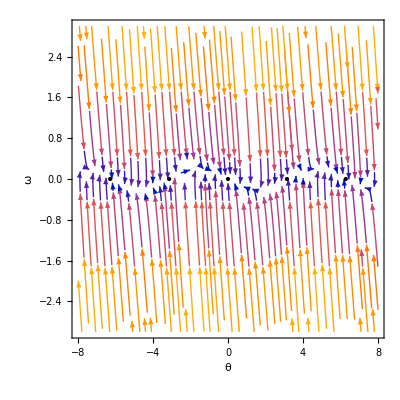

```mathematica
StreamPlot[{y,-5y-Sin[x]},{x,-8,8},{y,-3,3},StreamPoints->Fine,AspectRatio->1,Epilog->{PointSize->Large,Point[{{0,0},{π,0},{-π,0},{2π,0},{-2π,0},{3Pi,0},{-3Pi,0}}]},
	FrameLabel->{"θ","ω"}]
```

## Phase portrait of charged black hole

We first need to define the physical parameters/constants.

```mathematica
Clear[θ,M,Q,e,L]
θ=Pi/2;
M=1;
Q=0;
e = 1;
L = 1;
```

Now, let us define the R function and its relation with the derivative with respect to r

```mathematica
R[r_] = e^2/L^2 r^4-r^2+2*M*r-Q^2;
rdot2[r_]=R[r]/r^2;
rddot[r_]=Simplify[1/2*rdot2'[r]]
rdddot[r_]=Simplify[rddot'[r]];
```

-1/r^2+r

From here, we solve for the fixed points  by setting the first and second derivatives to zero.

```mathematica
sols=NSolve[rddot[2*M*r]==0,r,Reals]
```

{{r→0.5}}

Finally, we can plot the phase portrait and indicate the fixed points with a black dot.

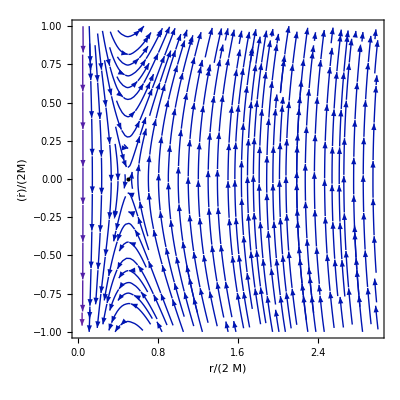

```mathematica
sols2=Select[r/. sols,Im[#]==0&];
myvars=Array[vars,Length@sols2];
Evaluate@myvars=sols2;
StreamPlot[{y/(2*M),rddot[2*M*x]/(2*M)},{x,0,3},{y,-1,1},StreamPoints->Fine,AspectRatio->1,Epilog->{PointSize[Large],(Point[{#,0}]&)/@(sols2)},
FrameLabel->{"r/(2  M)",OverDot["r"]/"2M"}]
```